```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}]; 
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

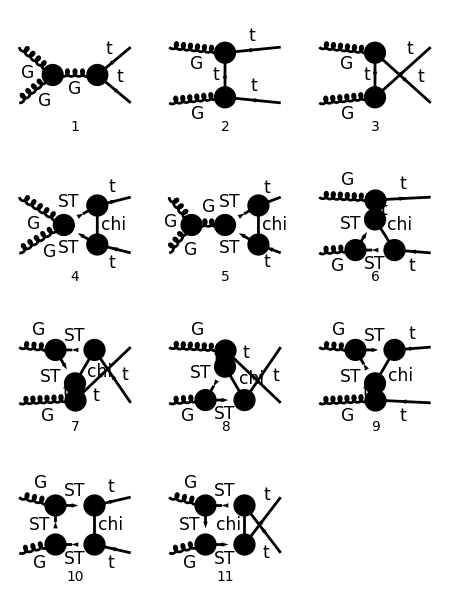

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
(* goodDiags=DiagramExtract[goodDiags,{1,5}]; *)
(* goodDiags=DiagramExtract[goodDiags,{10,11}]; *) 
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 450,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True, SheetHeader->None];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},TransversePolarizationVectors->{k1,k2}, LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames->{μ,ν}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
(* ampB = Normal[Series[ampA,{yDM,0,2}]]; *)
```

in total: 11 Particles amplitudes

```mathematica
ampC =Simplify[SUNSimplify[DiracSimplify[ TID[ampA,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True,DiracSimplify->False]]]];
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampD=Simplify[ampC-ampSM];
```

```mathematica
(* Remove higher order term *)
amp2=yDM^4 Coefficient[ampD,yDM,4];
ampE=Simplify[ampD-amp2];
```

```mathematica
(* Impose transversality relation to get rid of C0 terms *)
ampE=Collect[ampE,Cases2[ampE,C0],Simplify]/.{(Pair[Momentum[k2, D], Momentum[Polarization[k1, I, Transversality -> True], D]] - 
   Pair[Momentum[p1, D], Momentum[Polarization[k1, I, Transversality -> True], D]] - 
   Pair[Momentum[p2, D], Momentum[Polarization[k1, I, Transversality -> True], D]])->0};
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=Simplify[DiracSimplify[ampE]/.{s+t+u-> 2 MT^2}];
```

## Check Divergences

```mathematica
Table[{Cases2[ampEsimp,PaVe][[i]],PaXEvaluateUV[Cases2[ampEsimp,PaVe][[i]]]},{i,1,Length[Cases2[ampEsimp,PaVe]]}];
```

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[Coefficient[ampEsimp,deltaCTR]] (-1/(4 EpsilonUV));
```

```mathematica
FullSimplify[(loopUV+ctUV)]
```

0

## EFT Limit

```mathematica
(* Define global assumptions, valid in the EFT limit *)
$Assumptions={MT>0,mST>mChi,mST>0,mChi>0,mST>MT,mChi>MT,Im[s]==0,Im[t]==0,Im[u]==0,s>4MT^2};
```

```mathematica
(* Replace the propagators by explicit expressions with Mandelstam variables and A0,B0,C0 by PaVe*)
ampEFTa=FeynAmpDenominatorExplicit[ampEsimp];
```

#### Compute the EFT limit for the loop integrals (only C_00 has to be expanded up to order mt^2/s/t/u)

```mathematica
Cases2[ampEsimp,{A0,B0,C0}]
```

{}

```mathematica
loopInts =Cases2[ampEsimp,PaVe];
loopIntsEFT={};
Do[lInt =loopInts[[i]]/.{s->x^2 s,t-> x^2 t, u -> x^2 u, MT-> x MT};
If[FreeQ[lInt,PaVe[0,0,{a_,b_,c_},{d_,e_,f_},g___]],xorder=0,xorder=2];lIntEFT=Collect[PaXEvaluate[lInt,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{x,0,xorder}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi)),x->1},{Epsilon,s,t,u,MT},FullSimplify];
AppendTo[loopIntsEFT,{loopInts[[i]],lIntEFT}];
,{i,1,Length[loopInts]}];
```

#### Replace Counter - terms by their EFT expressions

```mathematica
deltaCTLeft=FullSimplify[Normal[Series[((1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])))//.{xT-> MT^2/mST^2,xC->mChi^2/mST^2,lA-> 1+xC^2+xT^2-2*xC-2*xT-2*xT*xC},{MT,0,0}]]]
deltaCTReft=FullSimplify[Normal[Series[((1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])))//.{xT-> MT^2/mST^2,xC->mChi^2/mST^2,lA-> 1+xC^2+xT^2-2*xC-2*xT-2*xT*xC},{MT,0,0}]]]+ (-1/(64 Pi^4 EpsilonUV))
```

0

-(-4 mChi^2 mST^2-4 mChi^4 log(mChi/mST)+3 mChi^4+mST^4)/(128 π^4 (mChi^2-mST^2)^2)-1/(64 π^4 ε_UV)

```mathematica
ampEFTb =ampEFTa/.Table[loopIntsEFT[[i,1]]-> loopIntsEFT[[i,2]],{i,1,Length[loopIntsEFT]}]/.{deltaCTL->deltaCTLeft,deltaCTR->deltaCTReft};
```

```mathematica
(* Make sure divergences were cancelled by the counter-terms *)
Coefficient[ampEFTb,Epsilon]
Coefficient[ampEFTb,EpsilonUV]
```

0

0

```mathematica
ampEFTc=SUNSimplify[DiracSimplify[ampEFTb/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

### Coefficients for each Term

```mathematica
spinorChains1=Tally[Cases[{ampEFTc},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEFTc},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEFTc},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2]]
pairs1=Cases2[ampEFTc,Pair]
su3prods=Join[Cases2[ampEFTc,SUNTF],Cases2[ampEFTc,SUNF]]
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2];
```

{(γ̄)^6,γ·k1,γ·k2,γ·ε(k1),γ·ε(k2)}

{k1·ε(k2),k2·ε(k1),p1·ε(k1),p1·ε(k2),p2·ε(k1),p2·ε(k2),ε(k1)·ε(k2)}

{T_Col3Col4^Glu5,(T^Glu1 T^Glu2)_Col3Col4,(T^Glu2 T^Glu1)_Col3Col4,f^Glu1Glu2Glu5}

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEFTc],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
If[Count[c,LorentzIndex[μ,D],Infinity]≠0,Continue[]];
If[Count[c,LorentzIndex[ν,D],Infinity]≠0,Continue[]];
c= Simplify[c/(I Pi^2 gs^2 yDM^2)];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEFTc]
```

(gs^2 yDM^2 (-(24 ⅈ 5 mChi^10)/(mST^2 (1)^6)+1730+(10 11(1))/(ε 5)))/(5760 π^2)
 |  |  |  |

```mathematica
su3Terms
```

{}

```mathematica
allPairs
```

{k1·ε(k2),k2·ε(k1),p1·ε(k1),p1·ε(k2),p2·ε(k1),p2·ε(k2),ε(k1)·ε(k2),(k1·ε(k2)) (k2·ε(k1)),(k1·ε(k2)) (p1·ε(k1)),(k1·ε(k2)) (p1·ε(k2)),(k1·ε(k2)) (p2·ε(k1)),(k1·ε(k2)) (p2·ε(k2)),(k1·ε(k2)) (ε(k1)·ε(k2)),(k2·ε(k1)) (p1·ε(k1)),(k2·ε(k1)) (p1·ε(k2)),(k2·ε(k1)) (p2·ε(k1)),(k2·ε(k1)) (p2·ε(k2)),(k2·ε(k1)) (ε(k1)·ε(k2)),(p1·ε(k1)) (p1·ε(k2)),(p1·ε(k1)) (p2·ε(k1)),(p1·ε(k1)) (p2·ε(k2)),(ε(k1)·ε(k2)) (p1·ε(k1)),(p2·ε(k1)) (p1·ε(k2)),(p1·ε(k2)) (p2·ε(k2)),(ε(k1)·ε(k2)) (p1·ε(k2)),(p2·ε(k1)) (p2·ε(k2)),(ε(k1)·ε(k2)) (p2·ε(k1)),(ε(k1)·ε(k2)) (p2·ε(k2))}

```mathematica
Coefficient[Expand[ampEFTc],su3prods[[1]]]
```

637+1/1+(gs^2 mST^6 yDM^2 1 (ε(k1)·ε(k2)) f^Glu1Glu2Glu5)/(288 (mChi^2-mST^2)^4 π^2)
 |  |  |  |

```mathematica
Cases2[%152,allTerms[[2]]]
```

{}